```mathematica
Quit[]
```

## Milking Truth level particle info (using -particles.csv)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MachineLearning`"]
```

```mathematica
datatotal=Table[Delete[Import["data/train_100_events/event00000"<>ToString[i]<>"-particles.csv"],1],{i,1000,1099,1}];
```

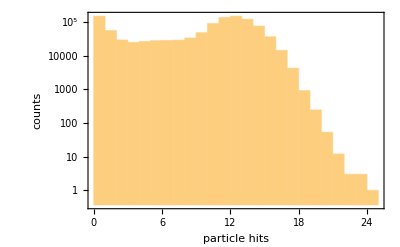

```mathematica
Histogram[#[[9]]&/@Flatten[datatotal,1],1000,"LogCount",Frame->True,FrameLabel->{"particle hits","counts"},PlotRange->{{0,25},Automatic}]
```

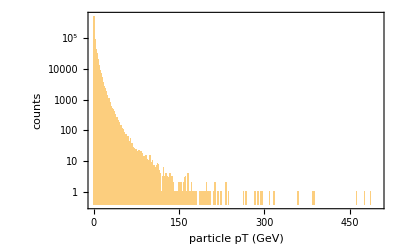

```mathematica
Histogram[Sqrt[#[[5]]^2+#[[6]]^2+#[[7]]^2]&/@Flatten[datatotal,1],1000,"LogCount",Frame->True,FrameLabel->{"particle pT (GeV)","counts"},PlotRange->{{0,500},Automatic}]
```

```mathematica
Count[#[[9]]&/@Flatten[datatotal,1],0]/Length[Flatten[datatotal,1]]//N
Count[#[[9]]&/@Flatten[datatotal,1],1]/Length[Flatten[datatotal,1]]//N
Count[#[[9]]&/@Flatten[datatotal,1],2]/Length[Flatten[datatotal,1]]//N
```

0.137462

0.051513

0.0270529

```mathematica
Histogram3D[{Sqrt[#[[5]]^2+#[[6]]^2],#[[9]]}&/@datatotal[[1]]]
```

-Graphics3D-

```mathematica
Histogram3D[{Sqrt[#[[5]]^2+#[[6]]^2+#[[7]]^2],#[[9]]}&/@datatotal[[1]]]
```

-Graphics3D-

```mathematica
Histogram3D[{Sqrt[#[[5]]^2+#[[6]]^2+#[[7]]^2],#[[9]]}&/@datatotal[[1]],40]
```

-Graphics3D-

```mathematica
Histogram3D[{Sqrt[#[[5]]^2+#[[6]]^2+#[[7]]^2],#[[9]]}&/@datatotal[[1]]]
```

-Graphics3D-

```mathematica
Histogram3D[{ArcTan[#[[6]]/#[[5]]],#[[9]]}&/@datatotal[[1]]]
```

-Graphics3D-

#### testing the initial coordination dependence

```mathematica
trainset=Flatten[datatotal[[1;;20]],1];
```

```mathematica
testset1=Flatten[datatotal[[21;;40]],1];
```

```mathematica
trainsetcoordinates={#[[2]],#[[3]],#[[4]]}&/@trainset;
trainsetlabels=If[#[[9]]≤1,#[[9]],7]&/@trainset;
```

```mathematica
testset1coordinates={#[[2]],#[[3]],#[[4]]}&/@testset1;
testset1labels=If[#[[9]]≤1,#[[9]],7]&/@testset1;
```

```mathematica
trainedclassifier=Classify[trainsetcoordinates->trainsetlabels]
```

ClassifierFunction[…]

```mathematica
trainsetcoordinates[[1]]
```

{-0.00928816,0.00986098,-0.0778789}

```mathematica
Length[trainsetlabels]
```

227182

```mathematica
trainvalidity=Table[trainedclassifier[trainsetcoordinates[[i]]]-trainsetlabels[[i]],{i,1,10000}];
```

```mathematica
testvalidity=Table[trainedclassifier[testset1coordinates[[i]]]-testset1labels[[i]],{i,1,10000}];
```

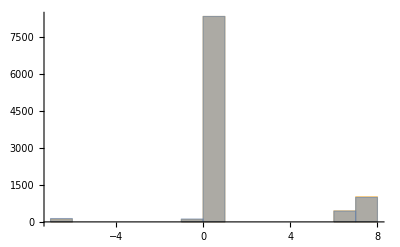

```mathematica
(*Having the particle coordination could lead to the correct guess rate to 83%, which has no difference from labeling all particle will have more than 1 tracks*)
Histogram[{trainvalidity,testvalidity}]
```

#### testing the initial momentum dependence

```mathematica
trainsetcoordinates={#[[5]],#[[6]],#[[7]]}&/@trainset;
trainsetlabels=If[#[[9]]≤1,#[[9]],7]&/@trainset;
```

```mathematica
testset1coordinates={#[[5]],#[[6]],#[[7]]}&/@testset1;
testset1labels=If[#[[9]]≤1,#[[9]],7]&/@testset1;
```

```mathematica
trainedclassifier=Classify[trainsetcoordinates->trainsetlabels]
```

ClassifierFunction[…]

```mathematica
trainvalidity=Table[trainedclassifier[trainsetcoordinates[[i]]]-trainsetlabels[[i]],{i,1,10000}];
```

```mathematica
testvalidity=Table[trainedclassifier[testset1coordinates[[i]]]-testset1labels[[i]],{i,1,10000}];
```

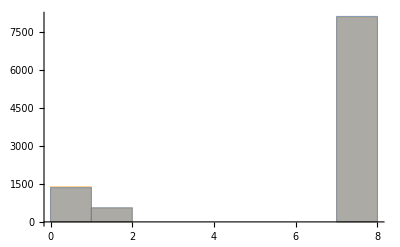

```mathematica
Histogram[{trainsetlabels[[1;;10000]],testset1labels[[1;;10000]]}]
```

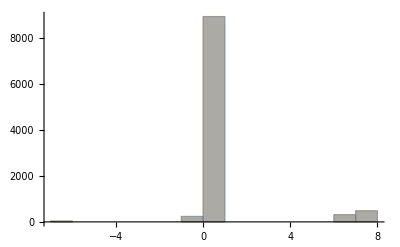

```mathematica
(*Having both the particle momentum could lead to the correct guess rate to 89%*)
Histogram[{trainvalidity,testvalidity}]
```

#### testing the initial momentum and coordination dependence

```mathematica
trainset=Flatten[datatotal[[1;;20]],1];
```

```mathematica
testset1=Flatten[datatotal[[21;;40]],1];
```

```mathematica
trainsetcoordinates={#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]]}&/@trainset;
trainsetlabels=If[#[[9]]≤1,#[[9]],7]&/@trainset;
```

```mathematica
testset1coordinates={#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]]}&/@testset1;
testset1labels=If[#[[9]]≤1,#[[9]],7]&/@testset1;
```

```mathematica
trainedclassifier=Classify[trainsetcoordinates->trainsetlabels]
```

ClassifierFunction[…]

```mathematica
trainvalidity=Table[trainedclassifier[trainsetcoordinates[[i]]]-trainsetlabels[[i]],{i,1,10000}];
```

```mathematica
testvalidity=Table[trainedclassifier[testset1coordinates[[i]]]-testset1labels[[i]],{i,1,10000}];
```

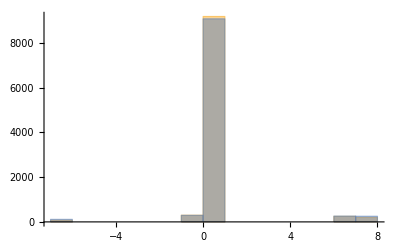

```mathematica
(*Having both the particle coordination and momentum could lead to the correct guess rate to 91%*)
Histogram[{trainvalidity,testvalidity}]
```

### Representation (after seeing machine can learn to have a 90% rate of guessing whether a particle should leave a hit or not physics should kick in)

```mathematica
pEpTeta[px_,py_,pz_]:={Sqrt[px^2+py^2+pz^2],Sqrt[px^2+py^2],Log[(Sqrt[px^2+py^2+pz^2]-Abs[pz])/(Sqrt[px^2+py^2+pz^2]+Abs[pz])]}
```

```mathematica
colors
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1., 0.77, 0.]}

```mathematica
coloreddatapEeta=Style[{pEpTeta[#[[5]],#[[6]],#[[7]]][[1]],pEpTeta[#[[5]],#[[6]],#[[7]]][[3]]},If[#[[9]]==0,colors[[1]],If[#[[9]]==1,colors[[2]],If[#[[9]]<=6,colors[[4]],colors[[3]]]]]]&/@trainset[[1;;10000]];
```

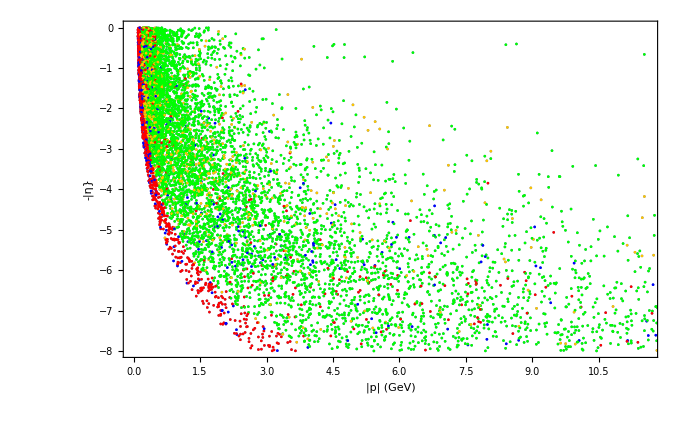

```mathematica
(*Red 0 hit; Blue 1 hit; Green 2-6 hits; Yellow > 6 hits*)
ListPlot[coloreddatapEeta,Frame->True,FrameLabel->{"|p| (GeV)","-|η}"}]
```

```mathematica
coloreddatapTeta=Style[{pEpTeta[#[[5]],#[[6]],#[[7]]][[2]],pEpTeta[#[[5]],#[[6]],#[[7]]][[3]]},If[#[[9]]==0,colors[[1]],If[#[[9]]==1,colors[[2]],If[#[[9]]<=6,colors[[4]],colors[[3]]]]]]&/@trainset[[1;;10000]];
```

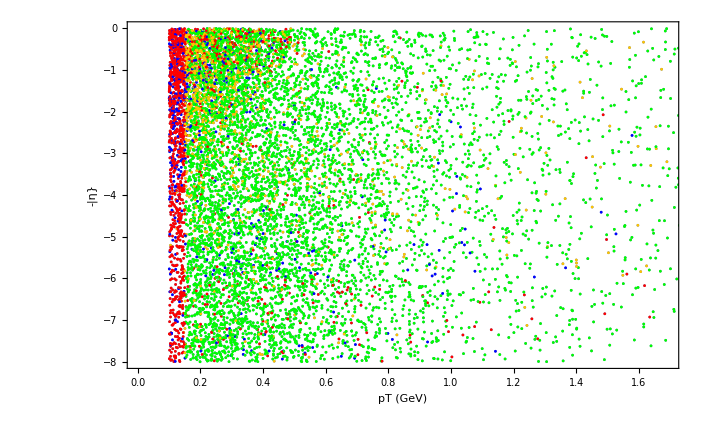

```mathematica
(*Red 0 hit; Blue 1 hit; Green 2-6 hits; Yellow > 6 hits*)
ListPlot[coloreddatapTeta,Frame->True,FrameLabel->{"pT (GeV)","-|η}"}]
```

## Understanding data a bit more

#### event 1000

```mathematica
SetDirectory["C:\\Users\\novar\\Desktop\\analysis"]
```

```mathematica
dataparticles=Import["train_100_events\\event000001000-particles.csv"];
datatrut=Import["train_100_events\\event000001000-truth.csv"];
datahits=Import["train_100_events\\event000001000-hits.csv"];
datacells=Import["train_100_events\\event000001000-cells.csv"];
```

```mathematica
Print[dataparticles[[1]]]
dataparticles=Delete[dataparticles,1];
Print[datatrut[[1]]]
datatrut=Delete[datatrut,1];
Print[datahits[[1]]]
datahits=Delete[datahits,1];
Print[datacells[[1]]]
datacells=Delete[datacells,1];
```

{particle_id,vx,vy,vz,px,py,pz,q,nhits}

{hit_id,particle_id,tx,ty,tz,tpx,tpy,tpz,weight}

{hit_id,x,y,z,volume_id,layer_id,module_id}

{hit_id,ch0,ch1,value}

```mathematica
groupedtruth=GroupBy[datatrut,#[[2]]&];
```

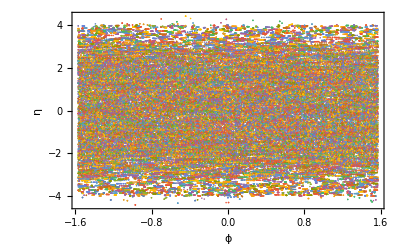

```mathematica
ListPlot[DeleteCases[Table[{ArcTan[#[[4]]/#[[3]]],1/2Log[(Sqrt[#[[3]]^2+#[[4]]^2+#[[5]]^2]-#[[5]])/(Sqrt[#[[3]]^2+#[[4]]^2+#[[5]]^2]+#[[5]])]}&/@groupedtruth[[i]],{i,2,Length[groupedtruth]}],Length[#]&≤3],Frame->True,FrameLabel->{"ϕ","η"},PlotRange->Full]
```

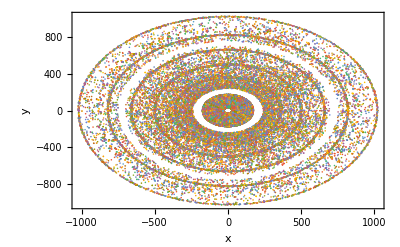

```mathematica
ListPlot[DeleteCases[Table[{#[[3]],#[[4]]}&/@groupedtruth[[i]],{i,2,Length[groupedtruth]}],Length[#]&≤3],Frame->True,FrameLabel->{"x","y"},PlotRange->Full]
```

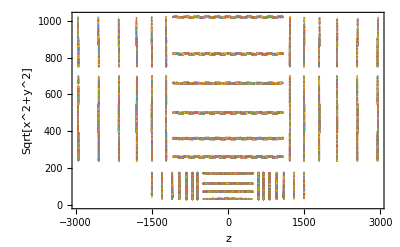

```mathematica
ListPlot[DeleteCases[Table[{#[[5]],Sqrt[#[[3]]^2+#[[4]]^2]}&/@groupedtruth[[i]],{i,2,Length[groupedtruth]}],Length[#]&≤3],Frame->True,FrameLabel->{"z","Sqrt[x^2+y^2]"},PlotRange->Full]
```

#### event 1001

```mathematica
SetDirectory["C:\\Users\\novar\\Desktop\\analysis"]
```

```mathematica
Needs["MachineLearning`"]
```

```mathematica
dataparticles=Import["train_100_events\\event000001001-particles.csv"];
datatrut=Import["train_100_events\\event000001001-truth.csv"];
datahits=Import["train_100_events\\event000001001-hits.csv"];
datacells=Import["train_100_events\\event000001001-cells.csv"];
```

```mathematica
Print[dataparticles[[1]]]
dataparticles=Delete[dataparticles,1];
Print[datatrut[[1]]]
datatrut=Delete[datatrut,1];
Print[datahits[[1]]]
datahits=Delete[datahits,1];
Print[datacells[[1]]]
datacells=Delete[datacells,1];
```

{particle_id,vx,vy,vz,px,py,pz,q,nhits}

{hit_id,particle_id,tx,ty,tz,tpx,tpy,tpz,weight}

{hit_id,x,y,z,volume_id,layer_id,module_id}

{hit_id,ch0,ch1,value}

```mathematica
groupedtruth=GroupBy[datatrut,#[[2]]&];
```

```mathematica
Length[datatrut]
Length[groupedtruth]
```

93680

7700

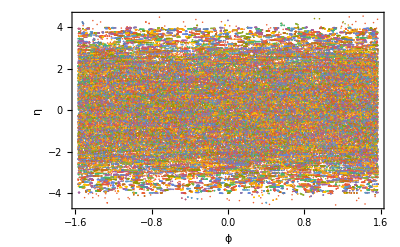

```mathematica
ListPlot[DeleteCases[Table[{ArcTan[#[[4]]/#[[3]]],1/2Log[(Sqrt[#[[3]]^2+#[[4]]^2+#[[5]]^2]-#[[5]])/(Sqrt[#[[3]]^2+#[[4]]^2+#[[5]]^2]+#[[5]])]}&/@groupedtruth[[i]],{i,2,Length[groupedtruth]}],Length[#]&≤3],Frame->True,FrameLabel->{"ϕ","η"},PlotRange->Full]
```

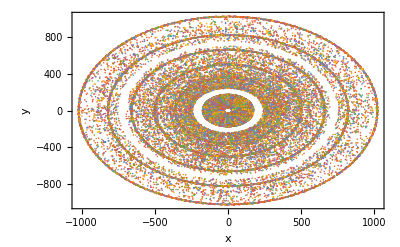

```mathematica
ListPlot[DeleteCases[Table[{#[[3]],#[[4]]}&/@groupedtruth[[i]],{i,2,Length[groupedtruth]}],Length[#]&≤3],Frame->True,FrameLabel->{"x","y"},PlotRange->Full]
```

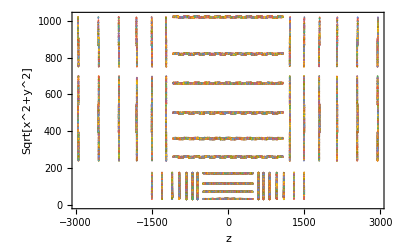

```mathematica
ListPlot[DeleteCases[Table[{#[[5]],Sqrt[#[[3]]^2+#[[4]]^2]}&/@groupedtruth[[i]],{i,2,Length[groupedtruth]}],Length[#]&≤3],Frame->True,FrameLabel->{"z","Sqrt[x^2+y^2]"},PlotRange->Full]
```

### Properties test

```mathematica
Table[{Length[groupedtruth[[i]]],Total[#[[9]]&/@groupedtruth[[i]]]},{i,2,1000}]
```

{{10,0.0000895073},{11,0.0000805177},{10,0.0000805177},{11,0.0000805177},{13,0.0000805177},{10,0.000103122},{11,0.0000805177},{14,0.0000805178},{11,0.0000805177}}